# 医学生物学分野における高被引用論文の長期変化

## 適用

* : 未稿

※ : 検討事項あり

## Manuscript

### Abstract*

### 0.0 intro（背景と目的）

計量書誌学においては3年インパクトファクターや5年インパクトファクターなど、特定の期間の被引用をもとにした指標が多く用いられる。これは一面的には評価の公正性を考慮したものと考えられる。つまり、より古い論文ほど被引用数は多くなり、この「論文の年齢」による効果を差し引くためである。一方で、被引用の長期変化もまた重要である。第一に、前述の公正性における評価期間の設定の根拠となる。次に、短期的には捉えられないよりマクロな変化を捉えるには真に長期の観察が必要である。このような問題に対し、本研究では主に後者の観点から長期にわたる引用関係から見えてくる現象を分析する。ここでの分析は単にインパクトの長期変化だけではなく研究テーマの変遷等も含むものである。マクロな変化を捉えるためには、長期的な観察のみならず大規模な対象が必要となる。従来、大規模な引用関係の分析は主に雑誌間の関係に注目されることが多かった。これは大規模な引用の要素をまとめる単位として雑誌が適当であることがおもな理由と考えられる。比較的大規模な研究としては、Leydesdorff[1,2,3,4]が雑誌間の関係マップを構築・調査した。天野ら[5,6]は医学生物学雑誌の大規模クラスタリングを行い、分野間の引用関係を明らかにした。近年ではLiら[7]が長期にわたる引用の特徴を、2300万論文をグループ化して調査した。しかしながら長期にわたる論文レベルの引用関係と研究のトレンドの変化に着目した研究は稀である。そこで本研究ではPubMedのデータを利用し長期にわたる引用・被引用の変化を調査した。特に高被引用論文は研究のトレンドをよく反映するものと考えられ、またPubMedには各論文に統制語が付与されているため、高被引用論文に付与される統制語を計量的に分析することにより、トレンド変化の特徴を見出せると期待される。また本研究では世代ごとのデータを累積的に構成した。これにより一過的なトレンドは現れにくくなると期待される。

### 0.1 literature review*

### 1. Materials

#### 1.1 データ

本研究ではFTP版のPubmed baseline (2023)[8]を利用する。PubMed annual baseline(2023)の論文登録数を表1に示す。本研究で対象とする論文は、図1に示す、1946年から2020年までに出版された論文およびそれらから引用された論文、約3000万件である。

表1

PubMed annual baselineのレコード数

論文数 | 雑誌数 | 最初の論文出版年 | 最後の論文出版年
36,555,430 | 36,943 | 1781 | 2024

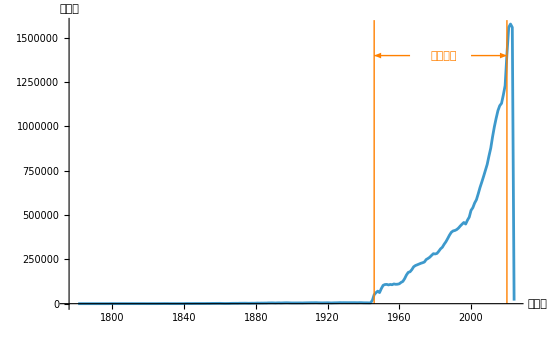

図1

PubMed annual baselineの登録論文数の推移

#### 1.2 主要論文・主要雑誌・主要テーマ

本研究においては、主要論文、主要雑誌、主要テーマの変化に注目する。主要論文とは「高被引用論文」のことであり、その定義は各累積世代において被引用数全体の1%を構成する論文集合とする。被引用数の1%に厳密に対応する論文集合の抽出は困難であるため、被引用数の多い順に論文の被引用数を累積し、全引用数の1%に最も近い順位を持つ論文までを対象とする。主要雑誌とは主要論文を出版した雑誌とする。主要テーマとは主要論文に付与されるMeSHの集合とする。さらに主要論文を引用する論文群を考え、これらの論文に付与されるMeSHの集合を主要引用テーマとする。また、主要テーマと主要引用テーマに関しては、比較のため高被引用ではない論文群のテーマについても分析する。対応するこれらをそれぞれ「研究テーマ」「引用テーマ」とする。主要テーマは研究テーマの一部であり、主要引用テーマは引用テーマの一部である。以上の定義をまとめたものを表2に示す。なお、テーマの計数には引用される論文のMeSHをそのままカウントする。一方、研究テーマと引用テーマの関係においては、論文1本とそれを引用する論文1本ごとに被引用側・引用側における完全2部グラフの関係とみなしエッジを分数カウントする。

表2

本研究での用語定義

主要論文 | 被引用数全体の1%を構成する被引用数上位論文（集合）。
主要雑誌 | 主要論文を出版した雑誌。
主要テーマ | 主要論文に付与されるMeSH。
主要引用テーマ | 主要論文を引用する論文に付与されるMeSH。
研究テーマ | 論文に付与されるMeSH。
引用テーマ | 論文を引用する論文に付与されるMeSH。主要引用テーマを含む
世代 | 1946 - 2020の期間に対して5年ごとに区切るもの。データを累積的に扱う場合は「累積世代」と表記する。

#### 1.3 世代の構成

本研究では時間的な変化を捉えるために世代を構成する。1946-2020の出版年をオーバーラップなしの5年ごとの区切りとし、15層の世代を構成する(表2)。各世代で対象となる被引用論文は、各世代の論文ではなくそれから引用される論文であり、 Pubmed baseline に収録される最初の出版年（1781）から当該世代までのすべてのタイプの記事である。本研究では累積的な変化に注目するため、これらの世代を累積的に用い、これを累積世代と称する。また、個別に用いる場合には単に世代と称する。

1946年以降の累積世代ごとの論文数、うち参照を持つ論文数、参照数（述べ）、被引用論文数（ユニーク）、登録雑誌数を図2に示す。登録雑誌数以外は指数関数的な増加を示している。

図 2

1946年以降の累積世代ごとの論文数

累積世代ごとの論文数(articles)、うち参照を持つ論文数(citing articles)、参照数(references)、被引用論文数(cited articles)、および雑誌数(Journal)の推移。

#### 1.4 比較グループ

3章と4章では高被引用論文群とその他の論文とを比較するため、主要論文のグループを含め全てで4グループを構成する。分割は順位ではなく生産性によるものとする。主要論文はすべての論文の総被引用数の1%を構成する論文群、つまり生産の上位0~1%の論文群であり、これをグループ1（G1）とする。同様に被引用数の25~26%を構成する論文をG2、50~51%を構成する論文をG3、75~76%を構成する論文をG4とする。

### 2. 高被引用論文と経年的な引用の効果（citation dynamics of highly cited papers）

#### 2.1 主要論文の出現数

主要論文の出現数を図3に示す。主要論文の全論文に占める割合と、新規主要論文の主要論文に占める割合をそれぞれ、図4、図5に示す。主要論文数および新規出現主要論文数は1946~2010年世代以降に急増している一方、主要論文の全論文に占める割合は一定の傾向を示していないことから、主要論文数の急増は収録論文数の急増を受けてのものであると考えられる。また、新規出現主要論文の主要論文に占める割合については一定の傾向は読み取れない。

-Graphics-

図3

累積世代ごとの主要論文および新規主要論文の出現数

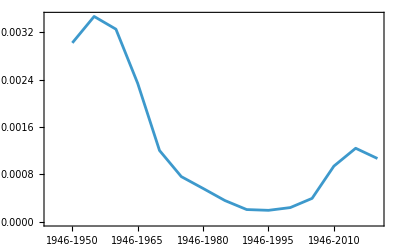

図4

累積世代ごとの主要論文の全論文に占める割合（%）

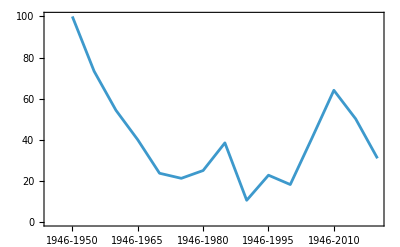

図5

累積世代ごとの新規出現主要論文の主要論文に占める割合（%）

#### 2.2 チャンピオン論文の変遷

累積世代ごとの最多被引用論文（チャンピオン論文）とその被引用数を表3に示す。チャンピオン論文は世代が進んでも引き続き引用され続ける傾向があり、数十年をかけてインパクトを上昇させている。このため最多被引用主要論文の交代は少ない。いずれの論文のテーマもタンパク質の分析に関するものであり、高被引用論文のテーマには嗜好性があることが示唆される。

表3

累積世代ごとの最多被引用論文タイトル

累積世代 | 論文タイトル | 収録誌タイトル | MeSH | 被引用数 | 当世代の
主要論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | - | 74 | 10
1946-1955 | Same as above | Same as above | Same as above | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 300 | 46
1946-1965 | Same as above | Same as above | Same as above | 1190 | 50
1946-1970 | Same as above | Same as above | Same as above | 3876 | 38
1946-1975 | Same as above | Same as above | Same as above | 9632 | 33
1946-1980 | Same as above | Same as above | Same as above | 17763 | 32
1946-1985 | Same as above | Same as above | Same as above | 25451 | 26
1946-1990 | Same as above | Same as above | Same as above | 32371 | 19
1946-1995 | Same as above | Same as above | Same as above | 37576 | 22
1946-2000 | Same as above | Same as above | Same as above | 40229 | 33
1946-2005 | Same as above | Same as above | Same as above | 42101 | 66
1946-2010 | Same as above | Same as above | Same as above | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | Autoradiography
Carbon Isotopes
Coliphages
Electrophoresis, Disc
Genes
Genetics, Microbial
Kinetics
Viral Proteins | 49961 | 315
1946-2020 | Same as above | Same as above | Same as above | 54249 | 336

#### 2.3 主要論文への経年的な引用の効果

ここで、主要論文への経年的な引用の効果を観察するためにオブソレッセンスを確認する。各累積世代の主要論文の総数は536であったが、ここからさらに十分にオブソレッセンスが観察される論文を選択するために、図6に示す3つの条件を設定した： 1. 出版年から十分な期間がある、2. ピーク期が十分に過ぎ去っている、3. 被引用の傾向が十分に低下している。以上の条件は、P.D.B Paroloら[9]およびD. Wangら[10]のオブソレッセンスモデルに基づく。この結果77論文が選択された。以降、これらの論文を主要obsolete論文と呼ぶ。

主要obsolete論文の経過年ごとの被引用数を図7に示す。出版からの経過年は最小で10年、最大で84年であった。同図からは近年の論文ほど出版直後から高い被引用を受ける傾向があることが窺える。主要obsolete論文および主要論文の出版からピークまでの年、ピークから減衰するまでの年（主要論文の場合は最終年まで）、出版から減衰するまでの年（主要論文の場合は最終年まで）を図8に示す。主要obsolete論文では出版からピークまでの年のモードは4年、ピークから減衰までの年のモードは7年、出版から減衰までの年のモードは12年であった。この結果は、P.D.B Paroloら、D. Wangらの既存の報告（出版後5年以内にピークが訪れる）を支持している。一方、十分な減衰が観察されなかった主要論文ではピーク年が10年付近であり異なる様相を示している。

次に、これら77論文の特徴を把握するために非階層クラスタリングを行った。クラスタリングに用いた特徴量は、a. 経過年に関する指標としてa-1:出版からピークまでの年（Peak period）、a-2:ピークから十分な減衰が見られるまでの年（Decay period）、b.生産性に関する指標としてb-1:ピーク年の被引用数（Peak count）、b-2:減衰年までの被引用数合計（Decay cited: A+B）、c.被引用の安定性に関する指標としてc-1:毎年の被引用数の分散（Variance:cited）、c-2:毎年の被引用速度の分散（Variance:diff）、c-3:毎年の引用加速度の分散（Variance:diff-accel）（以上、7指標）である。距離にはユークリッド距離を用い、各指標値にはノーマライズを行った。分散の計算においては先頭に0-パディングを使用した5年平均を用いた。この結果を図9に示す。クラスタリングでは明確なクラスは見受けられず、ノードが集中的に存在する領域といくつかのノードがまばらに見られる周辺領域が観察された。このことから主要obsolete論文の分布は比較的均質であることが窺える。

また、表1に示されるチャンピオンタイトルはいずれもオブソレッセンスの判定では陰性であった。これら3件の論文における、オブソレッセンスの判定に利用した指標を表4に、被引用数のプロットを図10に示す。いずれの論文も被引用のピークから十分な時間が経過している（Decay periodが十分に観測された）ものの、いまだに毎年十分な数の被引用がある。うち、2件の論文（Protein measurement with ... と Cleavage of structural proteins ...）については多峰性が見られ、被引用の傾向も似通っている。

表4

最多被引用論文タイトルにおけるオブソレッセンスにかかる指標

Title | Peak period
(year) | Decay period
(year) | Peak count | Decay cited | Variance:cited | Variance:diff | Variance:diff-accel
Qualitative analysis of ... | 9 | 5 | 23 | 177 | 28.4 | 1.2 | 0.6
Protein measurement with ... | 28 | 10 | 1740 | 29743 | 256971. | 5510.1 | 605.6
Cleavage of structural proteins ... | 23 | 5 | 2261 | 32245 | 380198. | 12712.1 | 1212.2

図6

主要論文のオブソレッセンスモデル、指標値および選択条件

図7

主要obsolete論文の被引用の傾向

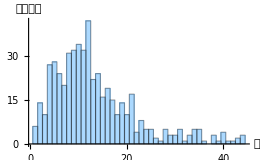
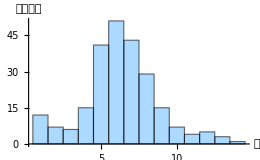
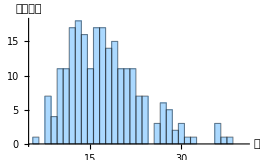
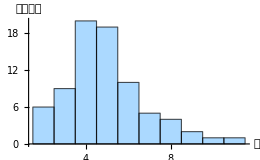
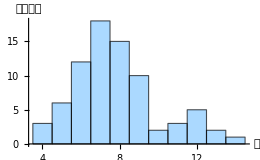
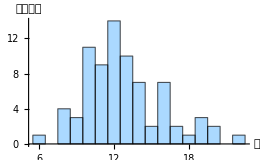
All | -Graphics- | -Graphics- | -Graphics-
Obsolate | -Graphics- | -Graphics- | -Graphics-

図8

主要obsolete論文および主要論文の主な指標年

「ピークから減衰までの年」および「出版から減衰までの年」については、減衰が観測された論文（239件）のみで集計した。

図9

主要obsolete論文のデンドログラム

標準化した7指標（前述）のユークリッド距離によるデンドログラムを構成し、PCA（PC1~PC3）プロットによる分布を確認した。メンバーが集中する領域（緑のドット）とそれ以外のメンバーが点在する領域（赤のドット）が見られる。デンドログラムの右端のメンバーが点在領域に位置するメンバー（ID:46,49,38,51,43）である。

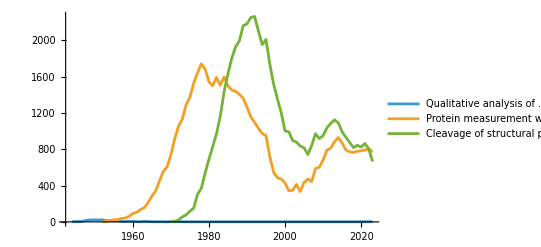

図10

最多被引用論文タイトルの被引用数の推移

3タイトルはいずれもオブソレッセンスが確認できなかった。また、うち2タイトルについては多峰性が見て取れる。

### 3. 主要雑誌の世代変化（evolution of core journals）

#### 3.1 主要雑誌の出現数

主要雑誌の出現数を図11に示す。主要雑誌の全雑誌に占める割合と、新規主要雑誌の主要雑誌に占める割合をそれぞれ、図12、図13に示す。主要雑誌数および新規出現主要論雑誌は1946~2010の世代以降に急増しており、前述した主要論文数の急増のタイミングと一致する。主要雑誌の全雑誌に占める割合および新規出現主要雑誌の主要雑誌に占める割合に一定の傾向は見られないが、主要論文のそれと同様の挙動が見られる。

-Graphics-

図11

累積世代ごとの主要雑誌および新規主要雑誌の出現数

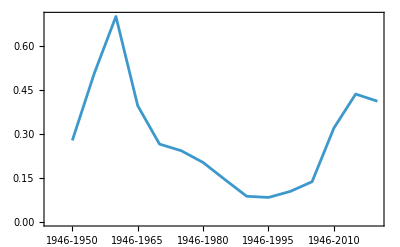

図12

累積世代ごとの主要雑誌の全雑誌に占める割合（%）

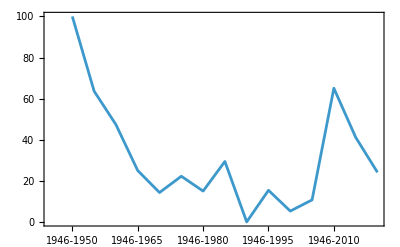

図13

累積世代ごとの新規出現主要雑誌の主要雑誌に占める割合（%）

#### 3.2 主要雑誌の変遷

ここでは主要雑誌の変化を高被引用でない論文群のそれと比較しながら分析する。累積世代ごとの代表論文を出版した雑誌のうち当該論文の出版数上位の一覧を表5-1~4に示す。各誌のインパクトファクター(IF)とその発表年についてはJournal Citation Report (JCR)[11]から求めた。JCRではインパクトファクターの公開が1997からであるため、1946-2000世代以降についてのみインパクトファクターを求めた。主要論文を持つ雑誌は必ずしもインパクトファクターが高い雑誌ではないことがわかる。表6は各グループ間の共通雑誌タイトルの構成比を求めたものである。これによれば、各グループとも2割から5割は他のグループと雑誌を共有しており、各グループが特定の雑誌群を構成しているわけでもない。

表5-1

累積世代ごとの主要雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
主要論文数 | 当該誌の主要論文が
当該世代主要論文に
占める割合(%) | 当該世代の
主要雑誌数 | IF | /IF発表年
1946-1950 | The Journal of clinical investigation
The Biochemical journal | 3
3 | 30 | 5 | 12.015/2000 | 15.053/2005 | 14.152/2010 | 12.575/2015 | 14.808/2020
4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1955 | The Biochemical journal | 13 | 43 | 11 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1960 | The Biochemical journal | 11 | 24 | 19 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1965 | The Biochemical journal | 13 | 26 | 16 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1970 | The Biochemical journal | 9 | 24 | 14 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1975 | The Journal of biological chemistry | 7 | 21 | 18 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1980 | The Journal of biological chemistry | 7 | 22 | 20 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1985 | The Journal of biological chemistry | 5 | 19 | 17 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1990 | The Journal of biological chemistry | 4 | 21 | 12 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1995 | The Journal of biological chemistry | 4 | 18 | 13 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-2000 | Journal of molecular biology
Proceedings of the National Academy of Sciences of the United States of America | 4
4 | 12 | 19 | 5.388/2000 | 5.229/2005 | 4.008/2010 | 4.517/2015 | 5.469/2020
10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 28 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America
Nature | 14
14 | 7 | 83 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2015 | Nature | 20 | 6 | 136 | 25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 145 | 3.409/2000 | 6.019/2005 | 4.877/2010 | 5.766/2015 | 6.937/2020

表5-2

累積世代ごとのG2雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G2論文数 | 当該誌のG2論文が
当該世代のメジャー論文
に占める割合(%) | IF / 発表年
1946-1950 | Journal of bacteriology | 34 | 45 | 3.506/2000 4.167/2005 3.726/2010 3.198/2015 3.49/2020
1946-1955 | The Biochemical journal | 20 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1960 | The Biochemical journal | 64 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | The Biochemical journal | 62 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1970 | The Journal of biological chemistry | 90 | 6 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of physiology | 98 | 5 | 4.455/2000 4.272/2005 5.139/2010 4.731/2015 5.182/2020
1946-1980 | The Journal of biological chemistry | 150 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 214 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | Proceedings of the National Academy of Sciences of the United States of America | 316 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1995 | Proceedings of the National Academy of Sciences of the United States of America | 410 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2000 | Proceedings of the National Academy of Sciences of the United States of America | 490 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 715 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 947 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2015 | Proceedings of the National Academy of Sciences of the United States of America | 882 | 5 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2020 | Proceedings of the National Academy of Sciences of the United States of America | 810 | 3 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020

表5-3

累積世代ごとのG3雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G3論文数 | 当該誌のG3論文が
当該世代のメジャー論文
に占める割合(%) | IF / 発表年
1946-1950 | The Biochemical journal | 41 | 24 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1955 | The Journal of biological chemistry | 21 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1960 | Proceedings of the Society for Experimental Biology and Medicine. Society for Experimental Biology and Medicine (New York, N.Y.) | 71 | 5 | 3.415/2000 -/2005 -/2010 -/2015 -/2020
1946-1965 | The Journal of biological chemistry | 72 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1970 | The Journal of biological chemistry | 116 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of biological chemistry | 205 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1980 | The Biochemical journal | 267 | 4 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 388 | 4 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | The Journal of biological chemistry | 440 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1995 | The Journal of biological chemistry | 782 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 897 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1419 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 1681 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | The Journal of biological chemistry | 1976 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2020 | The Journal of biological chemistry | 1678 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020

表5-4

累積世代ごとのG4雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G4論文数 | 当該誌のG4論文が
当該世代の論文
に占める割合(%) | IF / 発表年
1946-1950 | Annals of surgery | 34 | 10 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1955 | Annals of surgery | 105 | 6 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1960 | The Biochemical journal | 240 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | Nature | 121 | 3 | 25.814/2000 29.273/2005 36.104/2010 38.138/2015 49.962/2020
1946-1970 | British medical journal | 185 | 2 | 5.331/2000 9.052/2005 13.471/2010 -/2015 -/2020
1946-1975 | Biochimica et biophysica acta | 290 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1980 | Biochimica et biophysica acta | 489 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1985 | The Journal of biological chemistry | 627 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1990 | Biochimica et biophysica acta | 842 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1995 | The Journal of biological chemistry | 1142 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 1770 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1375 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 2093 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | PloS one | 3117 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020
1946-2020 | PloS one | 3560 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020

表6

グループ間の共通雑誌タイトルの割合（%）

| G1 | G2 | G3 | G4
G1 | 100 | 43 | 50 | 33
G2 | - | 100 | 50 | 20
G3 | - | - | 100 | 22
G4 | - | - | - | 100

### 4. 主要テーマの世代変化と特徴（evolution of research themes）

#### 4.1 主要テーマの出現数

累積世代ごとの主要テーマ（MeSHディスクリプター）のユニーク出現数を図14に示す。2023年MeSHディスクリプターの総数はおよそ30000であるが、累積世代における出現数は最大でも3000を超える程度であり集中が見られる。新規出現主要ディスクリプターの主要ディスクリプターに占める割合を図15に示す。1946-1955年世代に高い値が見られる理由は、前世代ではディスクリプター付与がほとんどなかったためである。累積世代ごとの主要テーマ出現の集中度を見るために求めたGini係数を図16に示す。累積世代が進むにつれ上昇する傾向にあるが最大でも0.6程度となる。

図14

累積世代ごとの主要論文に付与されたMeSHディスクリプターの種数

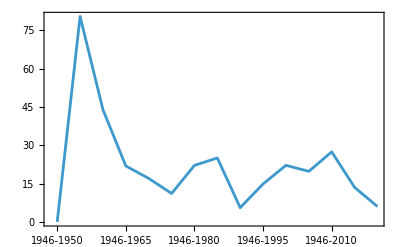

図15

新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）

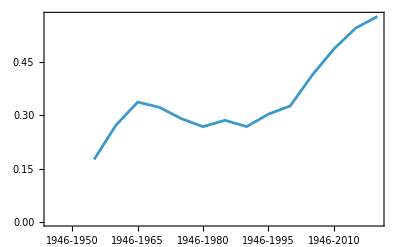

図16

累積世代ごとの主要論文に付与されたMeSHディスクリプターの出現数に関するジニ係数

1946~1950世代では当該ディスクリプターの付与がほとんどなかったため値を算出していない。

#### 4.2 主要テーマの変遷

ここでは主要テーマの変化を、高被引用でない論文群のテーマと比較する。テーマの計数については前述したように1論文対1論文の引用強度が1となるようにテーマ間の引用を分数計数とした。

各累積世代、各グループごとの最頻出テーマを表7に示す。最頻出テーマは研究テーマと引用テーマに分けた。最頻出テーマのバラエティは、高被引用グループの研究テーマにのみ見られ、それ以外のテーマはHumansもしくはAnimalsの出現のみでありバラエティは非常に低い。

次に、各累積世代のテーマ全体の多様性の変化を見るために各グループのエントロピーの変化を観察した。研究テーマ、引用テーマ、研究テーマと引用テーマの対の出現数のエントロピーを、それぞれ図17-1 ~ 図17-3に示す。図17からは主要論文グループのみが研究テーマのエントロピーが低く、その他のグループ間ではそれほど差がないことがわかる。なお、1946~1950世代に関してはディスクリプターの付与数が十分でなかったため除外している。

また、研究者の引用行動は必ずしも当該論文と同じ分野を引用するものではない。この転換の程度を見るために、グループごとに研究テーマと引用テーマのコサイン距離を観察した。この結果を図18に示す。こちらも高被引用グループのみが他とは異なる様相を示した。また、高被引用グループにおいても1946~2010世代以降は減少傾向にあり、他グループとの差は累積世代ごとに少なくなっている。各累積世代間の研究テーマも一定でなく世代ごとの嗜好の影響を受けると考えられる。この転換の程度を確認するために、各グループの累積世代間の研究テーマのコサイン距離を観察した。世代間では論文集合のメンバーが異なるので論文集合全体のテーマの重み付カウントを用いた。値は前世代との距離を表す。この結果を図19に示す。これによれば累積世代間のテーマの転換は観察されるものの一定の傾向を示さなかったが、グループ2のみが常に低いテーマ転換を保っていることから、被引用において中庸な一部の論文群においてはそのテーマが安定的である可能性が高い。

以上より、テーマの変遷には次の特徴があると考えられる：(1)高被引用論文は異なるテーマから引用されやすい。このことは表7の最頻出テーマから予想され、図18における転換の値もこれを裏付けている。(2)高被引用論文群は研究テーマが集中的であり、それを引用する論文群の研究テーマもまた集中的である。このことは図17から窺える。(3)高被引用論文のテーマの多様性は、共時的には低いが通時的には比較して高くなると思われる。このことは、図17-2では他のグループに比べ低いエントロピーが観察されるにもかかわらず、表7ではG1-Citedのテーマにはバラエティが見られることから窺える。(4)また、図14から、全体として研究テーマは各累積世代ごとの変遷は観察されるものの、その程度の傾向も一定ではない。

表7

累積世代ごと論文グループごとの最頻出テーマ

Citingは引用テーマ、Citedは研究テーマを示す。

1946-1955
1946-1960
1946-1965
1946-1970
1946-1975
1946-1980
1946-1985
1946-1990
1946-1995
1946-2000
1946-2005
1946-2010
1946-2015
1946-2020 | G1
Citing | 
Cited
Humans | Insulin
Humans | Blood Proteins
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Proteins
Animals | Proteins
Animals | Proteins
Animals | Base Sequence
Animals | Base Sequence
Animals | Base Sequence
Animals | Humans
Humans | Humans
Humans | Humans | G2
Citing | 
Cited
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Animals | Humans
Animals | Animals
Animals | Humans
Animals | Animals
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans | G3
Citing | 
Cited
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans | G4
Citing | 
Cited
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans

-Graphics--Graphics--Graphics-

図17

累積世代、論文グループごとのMeSHディスクリプターの出現に関するエントロピー

1946~1950世代では十分なディスクリプターの付与がなかったため対象外とした。

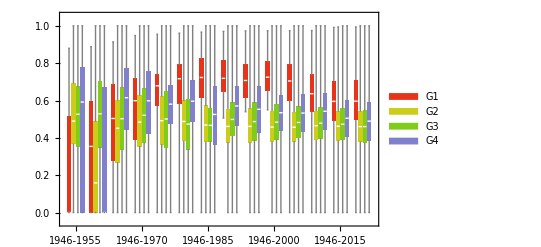

図18

累積世代、論文グループごとの研究テーマに対する引用テーマの転換

論文に付与されたディスクリプターとその論文を引用する論文に付与されたディスクリプター出現数ベクトルのコサイン距離。箱ひげ図の区間は、下から最小値、25%分位点、中央値、75%分位点、最大値となる。1946~1950世代では十分なディスクリプターの付与がなかったため対象外とした。

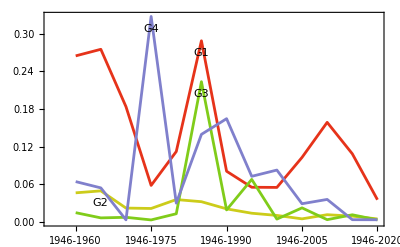

図19

累積世代間、論文グループごとの論文集合における累積世代間の研究テーマの転換

累積世代間における各グループのディスクリプター総出現数ベクトルのコサイン距離。
1946~1950世代では十分なディスクリプターの付与がなかったため対象外とした。

### 5. まとめ

高被引用論文の被引用数の順位変化とオブソレッセンス

本研究では高被引用論文を、累積的な引用による1%の被引用を構成する上位の論文とした（主要論文と呼ぶ）。これら主要論文は1945~2020世代においては全論文数の0.001%に相当する。主要論文はその被引用の累積的な効果により長期にわたり上位の順位を維持するものの、最終的にはオブソレッセンスにより新しい世代の論文にその座を明け渡す現象を確認できた。この累積的な効果は非常に長いものであり最長で50年以上のものが観察された。主要論文のうち十分なオブソレッセンスが観察されたものに限れば、被引用の変化の傾向（出版から被引用のピークまでのモードや被引用の長期変化の形状）は過去の報告を裏付けるものであった。一方で十分なオブソレッセンスが観察されないものでは出版から被引用のピークがより長期になる傾向が見られ、最上位の論文はこの傾向にある。

高被引用論文を輩出する雑誌の特徴

長期にわたる引用を考慮した、本研究の定義による高被引用論文は、必ずしも高いインパクトファクターの雑誌から輩出されるわけではないことが明らかになった。累積的な長期にわたる影響（被引用）をもつ論文を輩出する雑誌は、インパクトファクターを見れば3~50と幅広い。一方、これらの中によりハイインパクトな雑誌の出現は見られなかった。前述のオブソレッセンスモデルとの関係を考慮すれば、インパクトファクターが非常に高い雑誌には、被引用のピークが高くかつ早く訪れる論文が集中すると考えられ、そうでない雑誌にはそのような集中がないまたは弱い傾向にあると考えられる。

高被引用論文の研究テーマと高被引用論文を引用する論文のテーマ

高被引用論文群は、共時的（スナップショット）にはその研究テーマおよびそれを引用する論文のテーマのそれぞれの多様性は低いが、研究テーマ対それを引用する論文のテーマという観点ではバラエティ（転換）が高くなる。結果、通時的（長期）には研究テーマ=引用テーマ対の多様性は高くなると思われ、このことがオブソレッセンスを抑制しているのではないかと考えられる。言い換えれば、様々な分野から興味を持たれるようなテーマの論文は”長生き”すると考えられる。前述の雑誌の特徴と照らせば、主要雑誌に基礎分野や学際的分野の雑誌が見られる一方で医学や工学といった特定分野の雑誌が見られないことも、これを示唆している。

オープンアクセスとの関係（open access and impact）

論文へのアクセシビリティが高いほど多くの読者の目にふれる可能性が高くなると考えることは自然である。OA群と非OA群との間で被引用数に差があるか、全ての累積世代に現れるグループメンバーの集合に対して、グループ間および各グループ内における分散分析（ANOVA）によるボンフェローニ検定（p < 0.001）を行った。ただし主要obsolete論文においてはOA論文が1件であったため比較は行わなかった。グループ間においては有意差は検出されず、グループ内においてはG3及びG4において有意差が検出された（表8）。また、全ての場合においてOA化論文群の方が非OA化論文群よりも被引用数が大きかった。

次に、被引用数において差が有意であったグループG3及びG4において、OA群と非OA群において研究テーマに有意差があるかを、論文間の研究テーマベクトルの距離（コサイン距離）を用いて検定した。検定にはPermANOVA[]を用いた。OA群と非OA群においてデータ数に大きな隔たりがあるため、双方より100論文を30回ランダムサンプリングし、それぞれの検定において2000回の順列組み換えを行った。サンプリングにおいてp値は高い値（1.000 ~ 0.943）を示し、テーマ間の有意差は見られなかった。

表8

グループごとのOA/非OAにおける平均被引用数

| non-OA | OA
G1 | 4652 | 4753
G2 | 54 | 56
G3 | 20 | 21*
G4 | 8 | 9*

* p < ボンフェローニ検定においてp<0.001の有意差あり

## 参考

[1] Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

[2] Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Docu- mentation. 2004, Vol. 60, No. 4, p. 371-427.

[3] Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

[4] Leydesdorf L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports? Journal of the American Society for Information Science and Tech- nology. 2006, Vol. 57, No. 5, p. 601-613.

[5] 天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

[6] 天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

[7] Xin Li, Xuli Tang. How biomedical papers accumulated their clinical citations: a large-scale retrospective analysis based on PubMed. 2024. Vol 129, p. 3315–3339.

[8] PubMed https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2024.07.01)

[9] P.D.B. Parolo, et.al. Attention decay in science. Journal of Informatics. 2015. Vol.9, p.734-745.

[10] Dashun Wang, Chaoming Song, Albert-László Barabási. Quantifying Long-Term Scientific Impact. Science. 2013. Vol. 342, No. 127. DOI: 10.1126/science.1237825

[11] Journal Citation Report. https://jcr.clarivate.com/jcr/home . (accessed 2024.07.01)

## TODO

## 使わないことにした章

### X. 累積世代ごとのレファレンスネットワークの変化

#### 7.1 累積世代ごとのレファレンスネットワーク構造の変化

ここではレファレンスネットワーク構造の変化を計量的に観察する。レファレンスネットワークの構造として想定されるものは、下位分野に対応するいくつかのサブネットワークの構成である。サブネットワークに該当する構造として弱連結グラフ（Weakly connected graph: WCG）を利用する。弱連結グラフとは共引用もしくは書誌結合によって連結される論文集合である。累積世代ごとのWCGに関する各特徴量を表9にを示す。この表はレファレンス情報をもとに構成しているため、レファレンスを持たず引用もされない論文は集計されていない。そこで「Largest WCG vertices % (all articles)」には全論文から再計算した割合を示す。Zipfの係数aについても全論文から再計算したがほぼ変化が見られなかったため記載していない。

全体の傾向として累積世代が進むに伴いWCGの数も増加するが最大WCGのメンバー数も急増する。この相乗効果によりグループを構成するメンバー数の差はより顕著になる。このことはZipfの係数aが累積世代が進むごとに増加していることからもわかる。一方で最大WCGのサイズ（論文数）も累積世代が進むにつれ増加し、2020にはそのメンバー数は全論文の6割に達している。

表9

累積世代ごとのレファレンスネットワークの属性:

論文数、WCG数、最大WCGにおける論文数（そのパーセンテージ）、すべての論文を対象にした場合の最大WCGにおける論文数のパーセンテージ、WCGを構成する論文数におけるZipfの係数a。

Generation | WCG vertices | Lone vertices | WCG | Largest WCG vertices | Largest WCG vertices % | Largest WCG vertices % (all articles) | Zipf's a
1946-1950 | 25659 | 296336 | 2353 | 17910 | 69.8 | 5.4 | 7.51
1946-1955 | 106865 | 774662 | 3851 | 94830 | 88.7 | 10.9 | 11.26
1946-1960 | 230664 | 1203519 | 4624 | 216474 | 93.8 | 15.3 | 12.1
1946-1965 | 387646 | 1774556 | 5729 | 370660 | 95.6 | 17.3 | 13.4
1946-1970 | 635815 | 2542940 | 7020 | 615244 | 96.8 | 19.5 | 13.94
1946-1975 | 991194 | 3356424 | 8446 | 966113 | 97.5 | 22.3 | 13.13
1946-1980 | 1452803 | 4248958 | 9401 | 1425267 | 98.1 | 25.1 | 13.7
1946-1985 | 2022734 | 5222321 | 10026 | 1993398 | 98.5 | 27.6 | 14.18
1946-1990 | 2761367 | 6403037 | 10687 | 2730892 | 98.9 | 29.9 | 14.7
1946-1995 | 3715190 | 7594669 | 11361 | 3683220 | 99.1 | 32.7 | 15.4
1946-2000 | 4704818 | 9000206 | 12147 | 4670358 | 99.3 | 34.2 | 15.4
1946-2005 | 6388248 | 10294609 | 13000 | 6351561 | 99.4 | 38.2 | 17.27
1946-2010 | 9604916 | 10857321 | 13398 | 9568400 | 99.6 | 46.9 | 17.87
1946-2015 | 14351433 | 11071404 | 13643 | 14315982 | 99.8 | 56.4 | 18.64
1946-2020 | 20271870 | 11229183 | 14933 | 20235562 | 99.8 | 64.4 | 19.1

#### 7.2 レファレンスネットワークの成長の様相

ここでは累積世代間のネットワークの差分を見ることにより、レファレンスネットワークの成長を捉える。成長をノードの発生、エッジの発生、これらによるネットワーク全体の構造変化ととらえ、構造変化に関してはWCGの結合に注目する。ノードの発生については新規出版と同義であるため特に言及しない。以下ではエッジの発生とWCGの結合に関する次の項目を調査する。

新規に発生した引用数

新規に発生した引用により結合が発生した前世代WCG数

新規に発生した引用に関して異なる前世代WCGを結合(引用)する論文の数

新規に発生した引用により異なる前世代WCGと結合された前世代WCG数

調査結果を表9に示す。新規に発生する引用やWCGの結合に寄与する論文は出版される論文の増加にともない増加する傾向にある。一方、他のWCGと結合されるWCGの割合は幅があるものの一定の傾向を見せている。

表9

累積世代間のレファレンスネットワークの差分に関する属性

累積世代 | 新規に発生した引用数 | 新規に発生した引用のうち
主要論文に対する引用数(%) | 新規に発生した引用に関して
異なる前世代WCGを結合する論文の数 | 新規に発生した引用により
結合が発生した前世代WCG数 | 新規に発生した引用により
異なる前世代WCGと結合された前世代WCG数 | 前世代WCG数 | WCGの結合率
1955 | 148555 | 718 (0.5) | 1632 | 1280 | 909 | 2353 | 0.39
1960 | 291655 | 3109 (1.1) | 1942 | 1485 | 1185 | 3851 | 0.31
1965 | 445022 | 8846 (2.) | 1717 | 1297 | 1070 | 4624 | 0.23
1970 | 818629 | 26986 (3.3) | 1937 | 1411 | 1133 | 5729 | 0.2
1975 | 1369688 | 43178 (3.2) | 2240 | 1549 | 1306 | 7020 | 0.19
1980 | 1998678 | 54563 (2.7) | 2520 | 1716 | 1500 | 8446 | 0.18
1985 | 2821649 | 103101 (3.7) | 2480 | 1683 | 1478 | 9401 | 0.16
1990 | 4022714 | 230540 (5.7) | 2438 | 1553 | 1392 | 10026 | 0.14
1995 | 5715688 | 221170 (3.9) | 2345 | 1450 | 1310 | 10687 | 0.12
2000 | 6095490 | 153837 (2.5) | 1603 | 1147 | 1048 | 11361 | 0.09
2005 | 9616785 | 103356 (1.1) | 2553 | 1508 | 1353 | 12147 | 0.11
2010 | 27854672 | 221562 (0.8) | 6243 | 2576 | 2407 | 13000 | 0.19
2015 | 63696093 | 1530822 (2.4) | 11124 | 3404 | 3235 | 13398 | 0.24
2020 | 98878679 | 5603859 (5.7) | 11676 | 3472 | 3255 | 13643 | 0.24

## 検討

Essential journalsの過去のIF <- 困難

Clustering -> 可視化が困難なのでクラスタリングで工夫するしかない

article <- 困難かも

cited/citing -> modularityによるコミュニティ発見はできるかも

MeSH

journal

cited/citing

MeSH

MeSH

article cited/citing

article内共出現

Network構造分析

Networkにおけるcentralityの偏り

Network成長の可視化 (reference) <- なんらかの捨象・クラスタリングが必要 -> 難しい

article

Journal

MeSH

Essential articlesが構成する「Essential network」を抽出できるか？

グラフ(vertex)の差分に注目する

top 1%を元にネットワークを再構築する

メンバーのtop1%を考慮する

表6、7のタームの頻度を考慮する

ジニ計数 : 集中度がサチるので、別の指標の方がよい、尖度が良いか？

グラフ複雑性

```mathematica
graphRedundancyComplexity[g_Graph] := Module[{vc, ec, ecmean, etp},
  vc = VertexCount[g] // N;
  ec = EdgeCount[g] // N;
  ecmean = ec/(vc^2);
  etp = Entropy[AdjacencyMatrix[g] // Flatten] // N;
  (vc) (vc^ecmean) Exp[etp]
  ]
```

```mathematica
cyclomaticComolexity[eCount_,nCount_,wcgCount_]:=eCount-nCount+2wcgCount
```

## Post exec